Natural Language Understanding

We saw earlier how to use ctrl= to enter natural language input. Now we’re going to talk about how to set up functions that understand natural language.

Interpreter is the key to much of this. You tell Interpreter what type of thing you want to get, and it will take any string you provide, and try to interpret it that way.

Interpret the string "nyc" as a city:

```mathematica
Interpreter["City"]["nyc"]
```

New York City

“The big apple” is a nickname for New York City:

```mathematica
Interpreter["City"]["the big apple"]
```

New York City

Interpret the string "hot pink" as a color:

```mathematica
Interpreter["Color"]["hot pink"]
```

RGBColor[1., 0.4117647058823529, 0.7058823529411764]

Interpreter converts natural language to Wolfram Language expressions that you can compute with. Here’s an example involving currency amounts.

Interpret various currency amounts:

```mathematica
Interpreter["CurrencyAmount"][{"4.25 dollars","85 cents","3400 rupees","5 euros"}]
```

{4.25 $,85 ¢,3400 ₹,5 €}

Compute the total, doing conversions at current exchange rates:

```mathematica
Total[{Quantity["4.25", "USDollars"],Quantity[85, "USCents"],Quantity[3400, "IndianRupees"],Quantity[5, "Euros"]}]
```

52.96 $

Here’s another example, involving locations.

Interpreter gives the geo location of the White House:

```mathematica
Interpreter["Location"]["White House"]
```

GeoPosition[{38.8977,-77.0366}]

It can also work from a street address:

```mathematica
Interpreter["Location"]["1600 Pennsylvania Avenue, Washington, DC"]
```

GeoPosition[{38.8977,-77.0366}]

Interpreter handles many hundreds of different types of objects.

Interpret names of universities (which “U of I” is picked depends on geo location):

```mathematica
Interpreter["University"][{"Harvard","Stanford","U of I"}]
```

{Harvard University,Stanford University,University of Illinois at Urbana-Champaign}

Interpret names of chemicals:

```mathematica
Interpreter["Chemical"][{"H2O","aspirin","CO2","wolfram"}]
```

{water,aspirin,carbon dioxide,tungsten}

Interpret names of animals, then get images of them:

```mathematica
EntityValue[Interpreter["Animal"][{"cheetah","tiger","elephant"}],"Image"]
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-}
```

Interpreter interprets whole strings. TextCases, on the other hand, tries to pick out instances of what you request from a string.

Pick out the nouns in a piece of text:

```mathematica
TextCases["A sentence is a linguistic construct","Noun"]
```

{sentence,construct}

Pick out currency amounts:

```mathematica
TextCases["Choose between $5, €5 and ¥5000","CurrencyAmount"]
```

{$5,€5,¥5000}

You can use TextCases to pick out particular kinds of things from a piece of text. Here we pick out instances of country names in a Wikipedia article.

Generate a word cloud of country names from the current Wikipedia article on tourism:

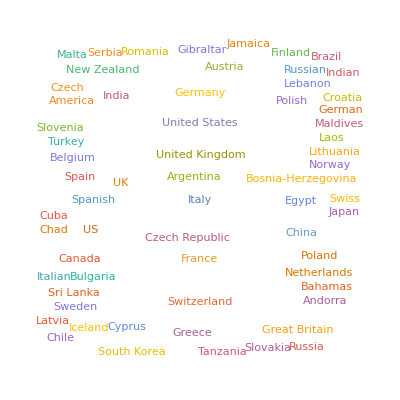

```mathematica
WordCloud[TextCases[WikipediaData["tourism"],"Country"]]
```

TextStructure shows you the whole structure of a piece of text.

Find how a sentence of English can be parsed into grammatical units:

```mathematica
TextStructure["You can do so much with the Wolfram Language."]
```

You
Pronoun
Noun Phrase  can
Verb  do
Verb  so
Adverbmuch
Adverb
Adverb Phrase  with
Preposition  the
DeterminerWolfram
Proper NounLanguage
Proper Noun
Noun Phrase
Prepositional Phrase
Verb Phrase
Verb Phrase.
Punctuation
Sentence

An alternative representation, as a graph:

```mathematica
TextStructure["You can do so much with the Wolfram Language.","ConstituentGraphs"]
```

{-Graphics-}

WordList[ ] gives a list of common words. WordList["Noun"], etc. give lists of words that can be used as particular parts of speech.

Give the first 20 in a list of common verbs in English:

```mathematica
Take[WordList["Verb"],20]
```

{aah,abandon,abase,abash,abate,abbreviate,abdicate,abduct,abet,abhor,abide,abjure,ablate,abnegate,abolish,abominate,abort,abound,abrade,abridge}

It’s easy to study properties of words. Here are histograms comparing the length distributions of nouns, verbs and adjectives in the list of common words.

Make histograms of the lengths of common nouns, verbs and adjectives:

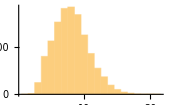
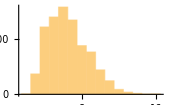
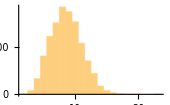

```mathematica
Histogram[StringLength[WordList[#]]]&/@{"Noun","Verb","Adjective"}
```

So far we’ve only talked about English. But the Wolfram Language also knows about other languages. For example, WordTranslation gives translations of words.

Translate “hello” into French:

```mathematica
WordTranslation["hello","French"]
```

{bonjour,hello,holà,ohé}

Translate into Korean:

```mathematica
WordTranslation["hello","Korean"]
```

{여보세요,안녕하세요}

Translate into Korean, then transliterate to the English alphabet:

```mathematica
Transliterate[WordTranslation["hello","Korean"]]
```

{yeoboseyo,annyeonghaseyo}

If you want to compare lots of different languages, give All as the language for WordTranslation. The result is an association which gives translations for different languages, with the languages listed roughly in order of decreasing worldwide usage.

Give translations of “hello” into the 5 most common languages in the world:

```mathematica
Take[WordTranslation["hello",All],5]
```

<|Mandarin→{表示問候的叫聲},Hindi→{हलो,नमस्ते},Spanish→{buenos días,hola},Russian→{привет,приветствие,Здравствуйте},Indonesian→{halo}|>

Let’s take the top 100 languages, and look at the first character in the first translation for “hello” that appears. Here’s a word cloud that shows that among these languages, “h” is the most common letter to start the word for “hello”.

For the top 100 languages, make a word cloud of the first characters in the word for “hello”:

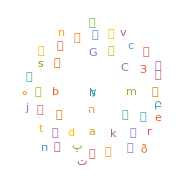

```mathematica
WordCloud[Values[StringTake[First[#],1]&/@Take[WordTranslation["hello",All],100]]]
```

Vocabulary

Interpreter["type"] |   | specify a function to interpret natural language 
TextCases["text","type"] |   | find cases of a given type of object in text 
TextStructure["text"] |   | find the grammatical structure of text 
WordTranslation["word","language"] |   | translate a word into another language

"15 Exercises Available" | "Get Started »"

Use Interpreter to find the location of the Eiffel Tower. »

| Expected output: |  
  | GeoPosition[{48.8583,2.29444}] |

Use Interpreter to find a university referred to as “U of T”. »

| Expected output: |  
  | "University of Toronto" |

Use Interpreter to find the chemicals referred to as C2H4, C2H6 and C3H8. »

| Expected output: |  
  | {"ethylene","ethane","propane"} |

Use Interpreter to interpret the date “20140108”. »

| Expected output: |  
  | "Wed 8 Jan 2014" |

Find universities that can be referred to as “U of X”, where X is any letter of the alphabet. »

| Expected output: |  
  | {"University of Birjand","University of Chicago","The University of Edinburgh","University of Georgia","University of Houston","University of Illinois at Urbana-Champaign","University of Lethbridge","University of Michigan-Ann Arbor","University of Phoenix-Online Campus","University of Regina","University of Saskatchewan","University of Toronto"} |

Find which US state capital names can be interpreted as movie titles (use CommonName to get the string versions of entity names). »

| Expected output: |  
  | {"Phoenix","Lincoln","Honolulu","Annapolis","Expedition: Bismarck","Providence","Nashville","Olympia","Madison"} |

Find cities that can be referred to by permutations of the letters a, i, l and m. »

| Expected output: |  
  | {"Lima","Ilam","Milah","Mali"} |

Make a word cloud of country names in the Wikipedia article on “gunpowder”. »

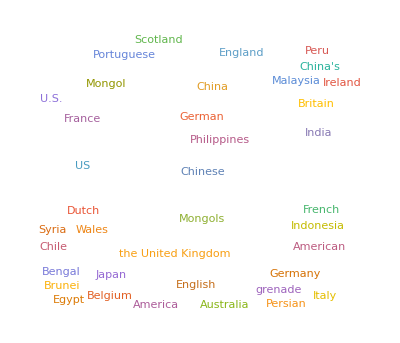
| Sample expected output: |  
  | -Graphics- |

Find all nouns in “She sells seashells by the sea shore.” »

| Expected output: |  
  | {"seashells","sea","shore"} |

Use TextCases to find the number of nouns, verbs and adjectives in the first 1000 characters of the Wikipedia article on computers. »

| Expected output: |  
  | {42,29,18} |

Find the grammatical structure of the first sentence of the Wikipedia article about computers. »

| Sample expected output: |  
  |  " " " ""A"
"Determiner""computer"
"Noun"
"Noun Phrase" " ""is"
"Verb" " " " ""a"
"Determiner""general-purpose"
"Adjective""device"
"Noun"
"Noun Phrase" " " " ""that"
"Determiner"
"Wh-Noun Phrase" " " " ""can"
"Verb" " ""be"
"Verb" " ""programmed"
"Verb" " " " ""to"
"Preposition" " ""carry"
"Verb" " ""out"
"Particle"
"Particle" " " " ""a"
"Determiner""set"
"Noun"
"Noun Phrase" " ""of"
"Preposition" " ""arithmetic"
"Noun""or"
"Conjunction""logical"
"Adjective""operations"
"Noun"
"Noun Phrase"
"Prepositional Phrase"
"Noun Phrase"
"Verb Phrase"
"Verb Phrase"
"Clause" " ""automatically"
"Adverb"
"Adverb Phrase"
"Verb Phrase"
"Verb Phrase"
"Verb Phrase"
"Clause"
"Clause"
"Noun Phrase"
"Verb Phrase""."
"Punctuation"
"Sentence" |

Find the 10 most common nouns in ExampleData[{"Text","AliceInWonderland"}]. »

| Expected output: |  
  | {"Rabbit","door","voice","time","Mouse","way","moment","thing","head","garden"} |

Make a community graph plot of the graph representation of the text structure of the first sentence of the Wikipedia article about language. »

| Sample expected output: |  
  | -Graphics- |

Make a list of numbers of nouns, verbs, adjectives and adverbs found by WordList in English. »

| Expected output: |  
  | {25133,6671,11520,3199} |

Generate a list of the translations of numbers 2 through 10 into French. »

| Expected output: |  
  | {"deux","trois","quatre","cinq","six","sept","huit","neuf","dix"} |

Q&A

What possible types of interpreters are there?

It’s a long list. Check out the documentation, or evaluate $InterpreterTypes to see the list.

Does Interpreter need a network connection?

In simple cases, such as dates or basic currency, no. But for full natural language input, yes.

When I say “4 dollars”, how does it know if I want US dollars or something else?

It uses what it knows of your geo location to tell what kind of dollars you’re likely to mean.

Can Interpreter deal with arbitrary natural language?

If something can be expressed in the Wolfram Language, then Interpreter should be able to interpret it. Interpreter["SemanticExpression"] takes any input, and tries to understand its meaning so as to get a Wolfram Language expression that captures it. What it’s doing is essentially the first stage of what Wolfram|Alpha does.

Can I add my own interpreters?

Yes. GrammarRules lets you build up your own grammar, making use of whatever existing interpreters you want.

Can I find the meaning of a word?

WordDefinition gives dictionary definitions.

Can I find what part of speech a word is?

PartOfSpeech tells you all the parts of speech a word can correspond to. So for “fish” it gives noun and verb. Which of these is correct in a given case depends on how the word is used in a sentence—and that’s what TextStructure figures out.

Can I translate whole sentences as well as words?

TextTranslation does this for some languages, usually by calling an external service.

What languages does WordTranslation handle?

It can translate lots of words for the few hundred most common languages. It can translate at least a few words for well over a thousand languages. LanguageData gives information on over 10,000 languages.

Tech Notes

TextStructure requires complete grammatical text, but Interpreter uses many different techniques to also work with fragments of text.

When you use ctrl= you can resolve ambiguous input interactively. With Interpreter you have to do it programmatically, using the option AmbiguityFunction.

More to Explore

Guide to Natural Language Interpreters in the Wolfram Language »